## Tesis

```mathematica
texto= Import[NotebookDirectory[]<>"Tesis.txt","Plaintext"];
texto = StringReplace[texto,WordBoundary~~Repeated[WordCharacter,4]~~WordBoundary->""];
texto = DeleteStopwords[texto];
```

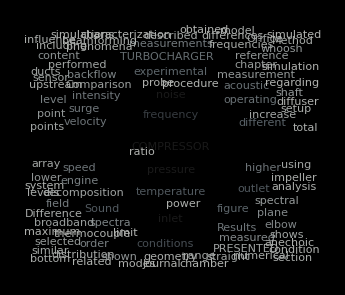

```mathematica
cloud= WordCloud[texto,ColorFunction->(ColorData["GrayTones"][0.75-#]&),ImageSize->Medium,ScalingFunctions->(#^1.2&)]
```

## Capitulos

#### Cap. liter

```mathematica
texto= Import[NotebookDirectory[]<>"cap_liter.tex","Text"];
```

```mathematica
texto = StringReplace[texto,WordBoundary~~Repeated[WordCharacter,4]~~WordBoundary->""];
```

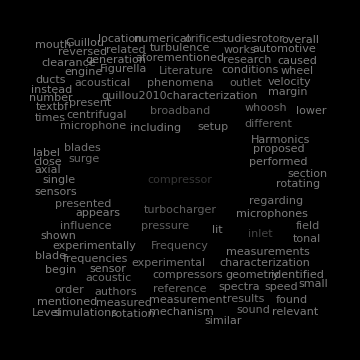

```mathematica
cloud= WordCloud[DeleteStopwords[texto],ColorFunction->(Blend[{GrayLevel[0.49],GrayLevel[0]},#1]&),ImageSize->Medium]
```

### Cap. method

```mathematica
texto= Import[NotebookDirectory[]<>"cap_metod.tex","Text"];
```

```mathematica
texto = StringReplace[texto,WordBoundary~~Repeated[WordCharacter,4]~~WordBoundary->""];
texto= StringReplace[texto,{
"figure"->"",
"mathbf"->"",
"label"->"",
"equation"->"",
"begin"->""
}];
```

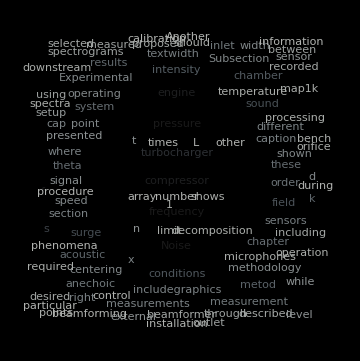

```mathematica
cloud= WordCloud[texto,ColorFunction->(ColorData["GrayTones"][0.75-#]&),ImageSize->Medium]
```